## Yukawa potential analysis

### Yukawa potential definition. Solve [-(∂^2+2/r ∂) /2μ - L(L+1)/2μ r^2 + U(r)/2μ ] ψ = k^2/2μ ψ ψ = u/r -> [-∂_r^2 + L(L+1)/r^2 + U(r) ] u = k^2 u

#### Solve for the regular solution near the origin for U(r) = -g/r E^(-r)

```mathematica
Clear[U,g]
U[g_,r_] = - g/r E^(-r);
```

```mathematica
Ueff[L_,g_,r_]=U[g,r]+L(L+1)/r^2;
```

#### resonances might be expected for L=1, g=6 or L=2, g=20.

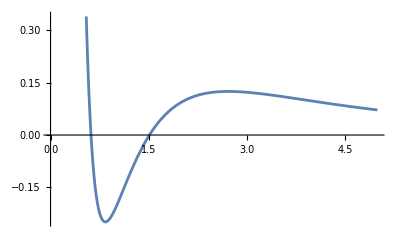

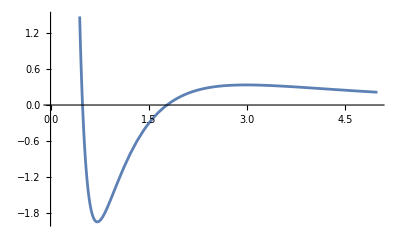

^6

```mathematica
Plot[Ueff[1,6,r],{r,0,5}]
Plot[Ueff[2,20,r],{r,0,5}]
```

### Solve the Schrodinger equation

```mathematica
Clear[u0,cc,eq,uinit,Duinit]
u0[L_,r_] =r^L( r + Sum[cc[n] r^n/n! ,{n,2,7}]);
eq[L_,r_,g_]=FullSimplify[Series[r^(-L)(-D[u0[L,r],{r,2}] + L(L+1)/r^2 u0[L,r] +U[g,r]u0[L,r] - k^2 u0[L,r]),{r,0,5}]]
```

(-g-(1+L) cc[2])+(g-k^2-1/2 g cc[2]-1/3 (3+2 L) cc[3]) r+1/12 (6 g cc[2]-6 k^2 cc[2]-2 g (3+cc[3])-3 (2+L) cc[4]) r^2+1/120 (-5 g (-4+6 cc[2]-4 cc[3]+cc[4])-4 (5 k^2 cc[3]+(5+2 L) cc[5])) r^3+1/360 (-15 k^2 cc[4]+15 g (-1+2 cc[2]-2 cc[3]+cc[4])-3 g cc[5]-5 (3+L) cc[6]) r^4+((-7 g (-6+15 cc[2]-20 cc[3]+15 cc[4]-6 cc[5]+cc[6])-6 (7 k^2 cc[5]+(7+2 L) cc[7])) r^5)/5040+O[r]^6

```mathematica
Clear[ccsol];ccsol[k_,g_]=FullSimplify[Solve[Table[SeriesCoefficient[eq[L,r,g],n]==0,{n,0,5}],Table[cc[n],{n,2,7}]],Assumptions->{L>=0, L∈Integers}][[1]]
```

{cc[2]→-g/(1+L),cc[3]→(3 g^2)/(2 (1+L))-(3 ((-1+g) g+k^2))/(3+2 L),cc[4]→-(g (g^2+2 (1+L) (3+2 L)-2 k^2 (4+3 L)+g (8+6 L)))/((1+L) (2+L) (3+2 L)),cc[5]→(5 (g^4+12 k^4 (1+L) (2+L)-4 g (-3+6 k^2-2 L) (1+L) (2+L)+4 g^3 (5+3 L)+g^2 (66-4 k^2 (5+3 L)+4 L (22+7 L))))/(4 (1+L) (2+L) (3+2 L) (5+2 L)),cc[6]→(3 g (-g^4-20 g^3 (2+L)-4 (1+L) (2+L) (3+2 L) (5+2 L)+8 k^2 (1+L) (5+2 L) (9+5 L)-4 k^4 (46+5 L (11+3 L))+2 g^2 (-173+10 k^2 (2+L)-10 L (19+5 L))+4 g (-156+2 k^2 (46+5 L (11+3 L))-L (283+L (163+30 L)))))/(4 (1+L) (2+L) (3+L) (3+2 L) (5+2 L)),cc[7]→(7 (g^6-120 k^6 (1+L) (2+L) (3+L)+10 g^5 (7+3 L)+8 g (1+L) (2+L) (3+L) (45 k^4+(3+2 L) (5+2 L)-5 k^2 (13+6 L))+2 g^4 (623-5 k^2 (7+3 L)+10 L (58+13 L))+4 g^3 (1551-2 k^2 (196+15 L (13+3 L))+L (2368+L (1153+180 L)))+4 g^2 (k^4 (196+15 L (13+3 L))-k^2 (1545+L (2551+2 L (653+105 L)))+2 (855+L (1901+L (1508+L (509+62 L)))))))/(8 (1+L) (2+L) (3+L) (3+2 L) (5+2 L) (7+2 L))}

#### initialization data

```mathematica
ccsol[k_,g_]={cc[2]->-g/(1+L),cc[3]->(3 g^2)/(2 (1+L))-(3 ((-1+g) g+k^2))/(3+2 L),cc[4]->-(g (g^2+2 (1+L) (3+2 L)-2 k^2 (4+3 L)+g (8+6 L)))/((1+L) (2+L) (3+2 L)),cc[5]->(5 (g^4+12 k^4 (1+L) (2+L)-4 g (-3+6 k^2-2 L) (1+L) (2+L)+4 g^3 (5+3 L)+g^2 (66-4 k^2 (5+3 L)+4 L (22+7 L))))/(4 (1+L) (2+L) (3+2 L) (5+2 L)),cc[6]->(3 g (-g^4-20 g^3 (2+L)-4 (1+L) (2+L) (3+2 L) (5+2 L)+8 k^2 (1+L) (5+2 L) (9+5 L)-4 k^4 (46+5 L (11+3 L))+2 g^2 (-173+10 k^2 (2+L)-10 L (19+5 L))+4 g (-156+2 k^2 (46+5 L (11+3 L))-L (283+L (163+30 L)))))/(4 (1+L) (2+L) (3+L) (3+2 L) (5+2 L))};
```

```mathematica
Clear[uinit,Duinit];
uinit[L_,r_,k_,g_] = u0[L,r]/.ccsol[k,g];
Duinit[L_,r_,k_,g_] = D[u0[L,r],r]/.ccsol[k,g];
```

#### Solve the differential equation, initializing at r0=1/100, out to rf = 20.

```mathematica
Clear[x,y,solution]
r0= 1/100;
rf=20;solution[L_,k_,g_]:=NDSolve[{-y'[r] + (L(L+1)/r^2+U[g,r]-k^2) x[r]==0,y[r]==x'[r],x[r0] ==uinit[L,r0,k,g],y[r0] == Duinit[L,r0,k,g]},{x,y},{r,r0,rf}  ][[1]]
```

#### project out the incoming and outgoing plane wave components

```mathematica
Clear[outwave]
outwave[L_,k_,g_]:=(uout = Evaluate[x[rf]/.solution[L,k,g]];duout = Evaluate[y[rf]/.solution[L,k,g]]; (-I)^L/2(duout/k + I uout)E^(- I k rf))
```

```mathematica
Clear[Smat,pcd]
Smat[L_,k_,g_]:=outwave[L,k,g]/Conjugate[outwave[L,k,g]];
pcd[L_,k_,g_] := -I k^(2L+1) (1+Smat[L,k,g])/(1-Smat[L,k,g]);
```

```mathematica
pcdtable[L_,g_]:=Chop[Table[{k,pcd[L,k,g]},{k,0.00001,3,.01}]];
```

## Plots of p^(2L+1) Cot[δ] for different L and g

### L=0

#### g=0.1, g=0.5, g=1, g=2, g=6

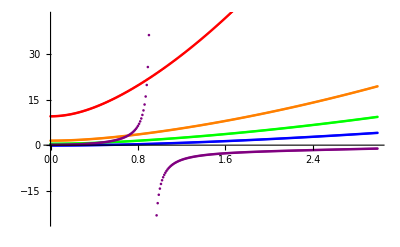

```mathematica
L0=0;ListPlot[{pcdtable[L0,.1],pcdtable[L0,.5],pcdtable[L0,1],pcdtable[L0,2],pcdtable[L0,6]},PlotStyle->{Red,Orange,Green,Blue,Purple}]
```

### L=1

#### g=0.1, g=0.5, g=1, g=2, g=6, g=10

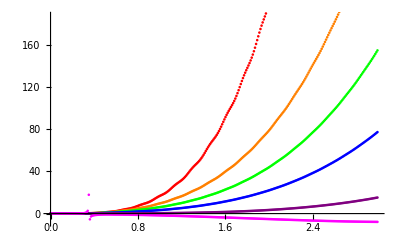

```mathematica
L0=1;ListPlot[{pcdtable[L0,.1],pcdtable[L0,.5],pcdtable[L0,1],pcdtable[L0,2],pcdtable[L0,6],pcdtable[L0,10]},PlotStyle->{Red,Orange,Green,Blue,Purple,Magenta}]
```

### L=2

#### g=0.1, g=0.5, g=1, g=2, g=6, g=20

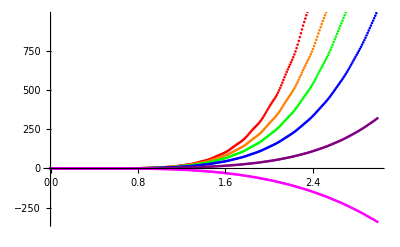

```mathematica
L0=2;ListPlot[{pcdtable[L0,.1],pcdtable[L0,.5],pcdtable[L0,1],pcdtable[L0,2],pcdtable[L0,6],pcdtable[L0,20]},PlotStyle->{Red,Orange,Green,Blue,Purple,Magenta}]
```